## Homework 1

### Problem 2.3

#### Graph

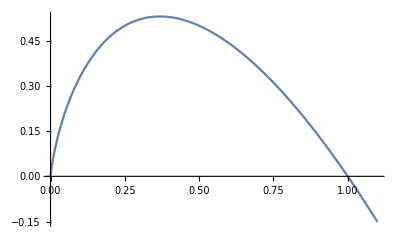

```mathematica
Plot[{-x Log[2,x]},{x,0,1.1}]
```

#### Functional Description

Define Simplification

```mathematica
FSc2p3[aa_]:=FullSimplify[aa,Assumptions->{pi∈Reals,pi≥0}]
```

Define Function

```mathematica
H[x_]:=-x Log[2,x]
```

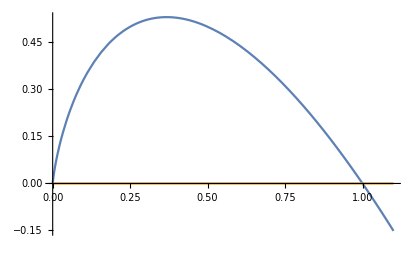

```mathematica
Plot[{H[x],H[x]+x Log[2,x]},{x,0,1.1}]
```

```mathematica
H[pi]//FSc2p3
```

-(pi Log[pi])/Log[2]

```mathematica
D[H[x],x]//FSc2p3
D[ D[H[x],x], x]//FSc2p3
```

-(1+Log[x])/Log[2]

-1/(x Log[2])

```mathematica
Solve[1==Log[2,x],x]
```

{{x→2}}

```mathematica
Log[2,ⅇ]//FSc2p3
```

1/Log[2]

```mathematica
FSc2p3[D[H[x],x]==-Log[2,ⅇ]-Log[2,x]]
```

True

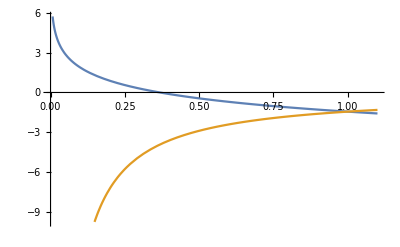

```mathematica
Plot[{FSc2p3[D[H[x0],x0]/.{x0->x}],FSc2p3[D[H[x0],{x0,2}]/.{x0->x}]},{x,0,1.1}]
```

```mathematica
Solve[{0==D[H[x],x]},x]
Solve[{1==D[H[x],x]},x]
Solve[{-Log[2,ⅇ]==D[H[x],x]},x]
```

{{x→1/ⅇ}}

{{x→1/(2 ⅇ)}}

{{x→1}}